2

-1

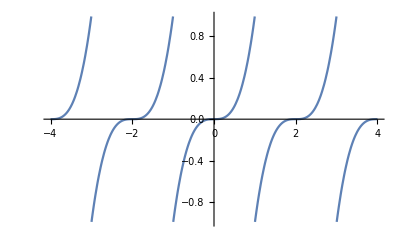

```mathematica
(*funcion a perdiodizar*)
F[x_]:= x^3;
(*periodo*)
periodo = 2
(*Offset*)
offset = -1(*<- el offset declara desde donde comienza Mod a trabajar en el eje x, 0 por Default.*)

(*Funcion periodizada*)
Fperiod[x_]:= F[Mod[x,periodo,offset]];
(*Grafo de la fucnion periodizada*)
Plot[Fperiod[x],{x,-2periodo,2periodo}]
```